```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bcl206/Documents/GitHub/hmm_movement/src

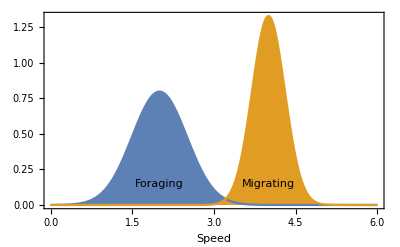

```mathematica
g=Show[Plot[{PDF[NormalDistribution[2, 0.5],x],PDF[NormalDistribution[4, 0.3],x]},{x,0,6},FillingStyle->Axis,Filling->Axis,Frame->{True,False,False,False},Axes->False,FrameTicks->None,FrameLabel->{"Speed"},LabelStyle->{Black,FontSize->16},Epilog->{Style[Text["Foraging", {2,0.15}],FontSize->16,White],Style[Text["Migrating", {4,0.15}],FontSize->16,White]}]]
```

```mathematica
Export["foraging_migrating.pdf",g]
```

foraging_migrating.pdf

```mathematica
Subscript[t,1]
```

t_1

```mathematica
ticks={{1,"t_1"},{2,"t_2"},{3,"t_3"}, {4,"t_4"}};
```

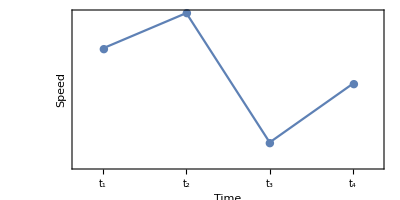

```mathematica
g2=ListLinePlot[{1, 1.3, 0.2, 0.7},Frame->{True,True,False,False},Axes->None,PlotRange->{{0.7,4.3},Full},PlotMarkers->{"●"},FrameLabel->{"Time", "Speed"},FrameTicks->{ticks,None},LabelStyle->{Black,FontSize->16},AspectRatio->1/2]
```

```mathematica
Export["hmm_time_series.pdf",g2]
```

hmm_time_series.pdf

## Longer series

```mathematica
p=HiddenMarkovProcess[{0.5,0.5},{{0.7,0.3},{0.25,0.75}},{NormalDistribution[2,0.5],NormalDistribution[4,0.3]}];
data=RandomFunction[p,{0,20}];
data1=(data//Normal)[[1]];
states=(FindHiddenMarkovStates[data,p]//Normal)[[1,All,2]];
state2=Flatten@Position[states, 2];
state1=Flatten@Position[states,1];
```

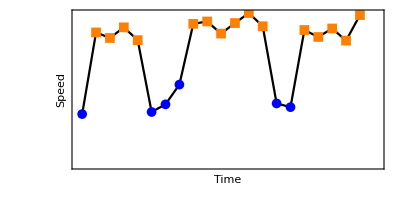

```mathematica
g2=Show[ListLinePlot[data,Frame->{True,True,False,False},Axes->None,PlotRange->{{-0.3,21.3},Full},FrameLabel->{"Time", "Speed"},FrameTicks->{None,None},LabelStyle->{Black,FontSize->16},AspectRatio->1/2,PlotStyle->Black],ListPlot[{data1[[state1]],data1[[state2]]},PlotStyle->{Blue,Orange},PlotMarkers->{Automatic, Medium}]]
```

```mathematica
Integrate[PDF[NormalDistribution[μ,σ],x]^0.5, {x,-∞,∞}]
```

$Aborted

## Multiple modes of movement: infinite HMMs

```mathematica
p=HiddenMarkovProcess[{1,0,0},{{0.7,0.29,0.01},{0.29,0.7,0.01},{0.02,0.01,0.97}},{NormalDistribution[2,0.5],NormalDistribution[4,0.3],NormalDistribution[6,0.3]}];
data=RandomFunction[p,{0,100}];
data1=(data//Normal)[[1]];
states=(FindHiddenMarkovStates[data,p]//Normal)[[1,All,2]];
state2=Flatten@Position[states, 2];
state1=Flatten@Position[states,1];
state3=Flatten@Position[states, 3];
```

```mathematica
states
```

{1,1,1,2,2,1,2,2,2,2,2,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,2,2,2,2,1,1,1,1,1,1,1,1,1,2,1,2,2,2,1,1,1,2,1,1,1,1,1,1,1,2,2,2,2,2,2,1,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
Manipulate[Show[ListLinePlot[data,Frame->{True,True,False,False},Axes->None,PlotRange->{{-0.3,a},Full},FrameLabel->{"Time", "Speed"},FrameTicks->{None,None},LabelStyle->{Black,FontSize->16},AspectRatio->1/2,PlotStyle->Black],ListPlot[{data1[[state1]],data1[[state2]],data1[[state3]]},PlotStyle->{Blue,Orange,Purple},PlotMarkers->{Automatic, Medium}]],{a,20,100}]
```

```mathematica
g=Table[Show[ListLinePlot[data,Frame->{True,True,False,False},Axes->None,PlotRange->{{-0.3,a},Full},FrameLabel->{"Time", "Speed"},FrameTicks->{None,None},LabelStyle->{Black,FontSize->16},AspectRatio->1/2,PlotStyle->Black],ListPlot[{data1[[state1]],data1[[state2]],data1[[state3]]},PlotStyle->{Blue,Orange,Purple},PlotMarkers->{Automatic, Medium}]],{a,20,100,1}];
```

```mathematica
Table[Export[StringJoin["../figures/cartoon/ihmm_",ToString@i, ".png"],g[[i]],ImageResolution->500],{i,1,Length@g,1}];
```

## Mixture models

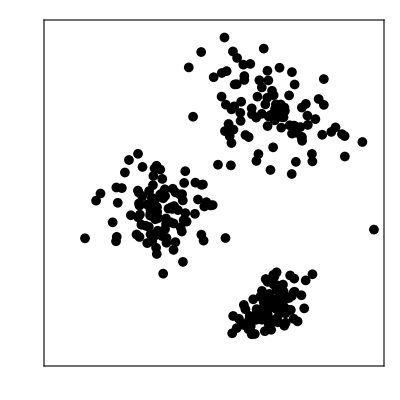

```mathematica
n=100;
μ1={0,0};
Σ1={{0.5,0},{0,0.5}};
μ2={3,3};
Σ2={{1,-0.5},{-0.5,1}};
μ3={3,-3};
Σ3={{0.2,0.1},{0.1,0.2}};
x1=RandomVariate[MultinormalDistribution[μ1,Σ1],n];
x2=RandomVariate[MultinormalDistribution[μ2,Σ2],n];
x3=RandomVariate[MultinormalDistribution[μ3,Σ3],n];
xmin=-3;
xmax=6;
ymin=-4.5;
ymax=5.5;
ppoints=50;
g1=Show[ContourPlot[PDF[MultinormalDistribution[μ1,Σ1],{x,y}],{x,xmin,xmax},{y,ymin,ymax},ContourShading->None,Contours->Function[{min,max},Range[min,max,0.05]],ContourStyle->Blue,PlotPoints->ppoints,PlotRange->Full,Axes->None,Ticks->None,FrameTicks->None],ContourPlot[PDF[MultinormalDistribution[μ2,Σ2],{x,y}],{x,xmin,xmax},{y,ymin,ymax},ContourShading->None,Contours->Function[{min,max},Range[min,max,0.05]],ContourStyle->Orange,PlotPoints->ppoints,PlotRange->Full,Axes->None,Ticks->None,FrameTicks->None],ContourPlot[PDF[MultinormalDistribution[μ3,Σ3],{x,y}],{x,xmin,xmax},{y,ymin,ymax},ContourShading->None,Contours->Function[{min,max},Range[min,max,0.1]],ContourStyle->Purple,PlotPoints->ppoints,PlotRange->Full,Axes->None,Ticks->None,FrameTicks->None]];
g2=Show[g1,ListPlot[{x1,x2,x3},PlotStyle->{Blue,Orange,Purple},PlotMarkers->{Automatic, Small}]];
g3=Show[ContourPlot[PDF[MultinormalDistribution[μ3,Σ3],{x,y}],{x,xmin,xmax},{y,ymin,ymax},ContourShading->None,Contours->Function[{min,max},Range[min,max,0.1]],ContourStyle->White,PlotPoints->ppoints,PlotRange->Full,Axes->None,Ticks->None,FrameTicks->None],ListPlot[{x1,x2,x3},PlotStyle->Black,PlotMarkers->{"●", Small}]]
```

```mathematica
Export["../figures/mixture_models_1.pdf",g1]
Export["../figures/mixture_models_2.pdf",g2]
Export["../figures/mixture_models_3.pdf",g3]
```

../figures/mixture_models_1.pdf

../figures/mixture_models_2.pdf

../figures/mixture_models_3.pdf